```mathematica
(* minimum set*)
```

```mathematica
Subscript[ss, 1]=({{0, 1}, {1, 0}});Subscript[ss, 2]=({{0, -I}, {I, 0}});Subscript[ss, 3]=({{1, 0}, {0, -1}});Subscript[ss, 4]=({{1, 0}, {0, 1}});QF3={{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)},{1/(2 √2),ⅇ^((ⅈ π)/4)/(2 √2),ⅈ/(2 √2),ⅇ^((3 ⅈ π)/4)/(2 √2),-1/(2 √2),ⅇ^(-(3 ⅈ π)/4)/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)},{1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2)},{1/(2 √2),ⅇ^((3 ⅈ π)/4)/(2 √2),-ⅈ/(2 √2),ⅇ^((ⅈ π)/4)/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅈ/(2 √2),ⅇ^(-(3 ⅈ π)/4)/(2 √2)},{1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2)},{1/(2 √2),ⅇ^(-(3 ⅈ π)/4)/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),ⅇ^((ⅈ π)/4)/(2 √2),-ⅈ/(2 √2),ⅇ^((3 ⅈ π)/4)/(2 √2)},{1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2)},{1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅈ/(2 √2),ⅇ^(-(3 ⅈ π)/4)/(2 √2),-1/(2 √2),ⅇ^((3 ⅈ π)/4)/(2 √2),ⅈ/(2 √2),ⅇ^((ⅈ π)/4)/(2 √2)}};B=N[ConjugateTranspose[QF3]];
```

```mathematica
VV3={{1,4,4},{4,2,4},{4,3,4},{4,1,4},{4,4,3},{4,3,3},{4,1,3},{1,1,4},{1,2,4},{3,4,2},{1,4,3}};
```

```mathematica
(*Circuit*)
```

```mathematica
G[i_,j_,k_,x_]:=N[MatrixExp[I x KroneckerProduct[Subscript[ss, i],Subscript[ss, j], Subscript[ss, k]]]]
```

```mathematica
Do[Do[Do[U=G[i,j,k,x];Subscript[A, i,j,k][x_]=N[U],{i,1,4}],{j,1,4}],{k,1,4}]
```

```mathematica
Ci[X_List]:=Subscript[A, 1,4,4][X[[7]]].Subscript[A, 4,3,3][X[[1]]].Subscript[A, 4,2,4][X[[8]]].Subscript[A, 1,1,4][X[[3]]].Subscript[A, 4,3,4][X[[9]]].Subscript[A, 1,2,4][X[[4]]].Subscript[A, 3,4,2][X[[5]]].Subscript[A, 1,4,3][X[[6]]].Subscript[A, 4,4,3][X[[10]]].Subscript[A, 4,1,3][X[[2]]].Subscript[A, 4,1,4][X[[11]]]
```

```mathematica
Ci2[X_List]:=Subscript[A, 1,4,4][X[[7]]].Subscript[A, 4,3,3][X[[1]]].Subscript[A, 4,2,4][X[[8]]].Subscript[A, 1,1,4][X[[3]]].Subscript[A, 4,3,4][X[[9]]].Subscript[A, 1,2,4][X[[4]]].Subscript[A, 3,4,2][X[[5]]].Subscript[A, 1,4,3][X[[6]]].Subscript[A, 4,4,3][X[[10]]].Subscript[A, 4,1,3][X[[2]]].Subscript[A, 4,1,4][X[[11]]].Subscript[A, 1,4,4][X[[12]]].Subscript[A, 4,3,3][X[[13]]].Subscript[A, 4,2,4][X[[14]]].Subscript[A, 1,1,4][X[[15]]].Subscript[A, 4,3,4][X[[16]]].Subscript[A, 1,2,4][X[[17]]].Subscript[A, 3,4,2][X[[18]]].Subscript[A, 1,4,3][X[[19]]].Subscript[A, 4,4,3][X[[20]]].Subscript[A, 4,1,3][X[[21]]].Subscript[A, 4,1,4][X[[22]]]
```

```mathematica
Ci3[X_List]:=Subscript[A, 1,4,4][X[[7]]].Subscript[A, 4,3,3][X[[1]]].Subscript[A, 4,2,4][X[[8]]].Subscript[A, 1,1,4][X[[3]]].Subscript[A, 4,3,4][X[[9]]].Subscript[A, 1,2,4][X[[4]]].Subscript[A, 3,4,2][X[[5]]].Subscript[A, 1,4,3][X[[6]]].Subscript[A, 4,4,3][X[[10]]].Subscript[A, 4,1,3][X[[2]]].Subscript[A, 4,1,4][X[[11]]].Subscript[A, 1,4,4][X[[12]]].Subscript[A, 4,3,3][X[[13]]].Subscript[A, 4,2,4][X[[14]]].Subscript[A, 1,1,4][X[[15]]].Subscript[A, 4,3,4][X[[16]]].Subscript[A, 1,2,4][X[[17]]].Subscript[A, 3,4,2][X[[18]]].Subscript[A, 1,4,3][X[[19]]].Subscript[A, 4,4,3][X[[20]]].Subscript[A, 4,1,3][X[[21]]].Subscript[A, 4,1,4][X[[22]]].Subscript[A, 1,4,4][X[[23]]].Subscript[A, 4,3,3][X[[24]]].Subscript[A, 4,2,4][X[[25]]].Subscript[A, 1,1,4][X[[26]]].Subscript[A, 4,3,4][X[[27]]].Subscript[A, 1,2,4][X[[28]]].Subscript[A, 3,4,2][X[[29]]]
```

```mathematica
Cost[X_List]:=1-1/64 Abs[Tr[Ci[X].B]]^2
```

```mathematica
Graa[W_List,NN_,dl_]:=(
uy={};Do[uO={};Do[uO=Append[uO,dl KroneckerDelta[i,j]],{j,1,NN}];uy=Append[uy, {(Cost[W+uO]-Cost[W-uO])/(2dl)}],{i,1,NN}];
Return[uy]);
```

```mathematica
NN=11;NM=10;koko={};loko={}; Do[L0={};Do[If[i==NN,joy={0,Pi},joy={0,Pi}];L0=Append[L0, RandomReal[joy]],{i,1,NN}];
di=Cost[L0];Print["Initial distance=",di];
ko=di; stro=0.5;stre=stro;
Do[
L=L0-stre Transpose[Graa[L0,NN,0.05]][[1]];ki=Cost[L];koko=Append[koko,ki];If[ki<ko,(*Print["!"];*)L0=L;If[Abs[ki-ko]< 10^-5,Goto[er]];ko=ki, (*If[Abs[ki-ko]< 10^-3,Goto[er]];*)stre=stre 0.8],{i,1,800}];(*Print[ko];*)Label[er];loko=Append[loko,L0];KO=Min[koko];Print[ko,L0],{kk,1,NM}]
```

Initial distance=0.983891

0.603744{3.17462,3.01117,2.06972,1.51696,0.735266,0.980392,1.23295,0.581216,1.29633,3.69502,1.16915}

Initial distance=0.98014

0.603745{0.0386507,3.42592,-0.0256003,1.76035,0.728867,0.980404,2.14179,2.15115,2.92385,1.21777,1.16822}

Initial distance=0.998593

0.603741{3.17556,0.767755,1.9788,0.281275,2.41408,2.55068,0.130449,2.15193,1.55059,3.22965,1.1725}

Initial distance=0.992159

0.603741{0.0389802,1.34989,0.96508,3.03201,0.734869,0.980694,0.6002,2.15703,1.8362,1.1863,2.74181}

Initial distance=0.951717

0.603742{0.0367053,0.0821225,0.250645,3.22175,2.40636,2.55124,0.718628,0.58917,0.274024,1.06775,1.17546}

Initial distance=0.971804

0.60374{3.17566,1.66861,-0.231604,1.65791,0.733573,0.980302,1.53515,2.15092,2.8747,3.39345,2.73885}

Initial distance=0.955993

0.750094{0.7501,0.132123,1.10381,2.9065,1.58287,1.80456,0.686189,1.17561,0.335331,0.8844,1.20322}

Initial distance=0.970809

0.603741{3.17598,1.96106,1.6483,1.34598,0.730515,0.980155,0.849956,2.14913,0.172837,2.50901,1.16757}

Initial distance=0.890117

0.603742{1.60611,2.3386,0.411229,0.279956,0.732242,2.55112,2.88319,-0.579023,1.55559,2.04591,2.73771}

Initial distance=0.996032

0.603742{3.17497,1.68479,-0.2136,-0.0957614,0.734316,0.980343,2.97101,2.15136,1.30713,3.52811,1.16858}

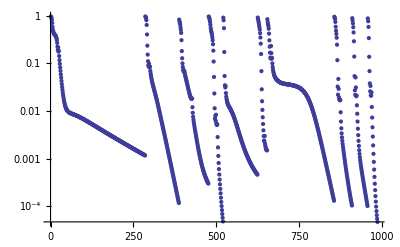

```mathematica
ListLogPlot[koko,PlotRange->All]
```

```mathematica
dd=Dimensions[loko][[1]];oups={};Do[L1=loko[[i]];ba=Cost[L1];la=N[Count[ba,0]/Dimensions[ba][[1]]];Print[i,"__",la];oups=Append[oups,la],{i,1,dd}]
```

```mathematica
(*29*)Min[koko]
```

0.0000464613

```mathematica
(*22*)Min[koko]
```

0.0380792

```mathematica
(*11*)Min[koko]
```

0.603733

```mathematica
(* let's take other gates*)
```

```mathematica
CiR[X_List]:=Subscript[A, 1,4,4][X[[7]]].Subscript[A, 4,3,2][X[[1]]].Subscript[A, 4,2,4][X[[8]]].Subscript[A, 1,3,4][X[[3]]].Subscript[A, 4,3,4][X[[9]]].Subscript[A, 1,3,4][X[[4]]].Subscript[A, 3,4,3][X[[5]]].Subscript[A, 1,4,2][X[[6]]].Subscript[A, 4,4,3][X[[10]]].Subscript[A, 4,1,1][X[[2]]].Subscript[A, 4,1,4][X[[11]]]
```

```mathematica
Ci3R[X_List]:=Subscript[A, 1,4,4][X[[7]]].Subscript[A, 4,3,2][X[[1]]].Subscript[A, 4,2,4][X[[8]]].Subscript[A, 1,3,4][X[[3]]].Subscript[A, 4,3,4][X[[9]]].Subscript[A, 1,3,4][X[[4]]].Subscript[A, 3,4,3][X[[5]]].Subscript[A, 1,4,2][X[[6]]].Subscript[A, 4,4,3][X[[10]]].Subscript[A, 4,1,1][X[[2]]].Subscript[A, 4,1,4][X[[11]]].Subscript[A, 1,4,4][X[[12]]].Subscript[A, 4,3,2][X[[13]]].Subscript[A, 4,2,4][X[[14]]].Subscript[A, 1,3,4][X[[15]]].Subscript[A, 4,3,4][X[[16]]].Subscript[A, 1,3,4][X[[17]]].Subscript[A, 3,4,3][X[[18]]].Subscript[A, 1,4,2][X[[19]]].Subscript[A, 4,4,3][X[[20]]].Subscript[A, 4,1,1][X[[21]]].Subscript[A, 4,1,4][X[[22]]].Subscript[A, 1,4,4][X[[23]]].Subscript[A, 4,3,3][X[[24]]].Subscript[A, 4,2,4][X[[25]]].Subscript[A, 1,1,4][X[[26]]].Subscript[A, 4,3,4][X[[27]]].Subscript[A, 1,2,4][X[[28]]].Subscript[A, 3,4,2][X[[29]]]
```

```mathematica
Cost[X_List]:=1-1/64 Abs[Tr[Ci3R[X].B]]^2
```

```mathematica
NN=29;NM=10;koko={};loko={}; Do[L0={};Do[If[i==NN,joy={0,Pi},joy={0,Pi}];L0=Append[L0, RandomReal[joy]],{i,1,NN}];
di=Cost[L0];Print["Initial distance=",di];
ko=di; stro=0.5;stre=stro;
Do[
L=L0-stre Transpose[Graa[L0,NN,0.05]][[1]];ki=Cost[L];koko=Append[koko,ki];If[ki<ko,(*Print["!"];*)L0=L;If[Abs[ki-ko]< 10^-5,Goto[er]];ko=ki, (*If[Abs[ki-ko]< 10^-3,Goto[er]];*)stre=stre 0.8],{i,1,800}];(*Print[ko];*)Label[er];loko=Append[loko,L0];KO=Min[koko];Print[ko,L0],{kk,1,NM}]
```

Initial distance=0.990025

0.0746958{2.35619,1.5653,1.93031,2.38938,3.92699,0.785238,0.19635,0.000670122,2.74889,0.785398,0.78662,3.13795,2.35619,1.41135,2.32442,2.35663,2.38795,2.74887,0.785398,2.35619,2.35533,-0.159448,2.36153,0.785398,0.785399,1.57098,2.74889,0.000183405,2.36156}

Initial distance=0.992711

0.410159{0.347644,1.57509,1.66607,1.86815,0.785416,1.56705,1.76722,1.57141,0.856406,1.32522,1.57131,1.556,2.35618,0.797348,0.521718,3.21303,1.04933,2.67337,1.57445,1.5708,2.9887,2.03107,1.58078,3.14173,3.07365,2.32097,1.96285,1.52235,0.791793}

Initial distance=0.973176

0.0746973{2.35619,0.785398,1.72503,2.59466,2.35619,2.35619,3.33794,4.21752×10^-10,3.53429,3.14159,2.35619,3.13776,3.13579,3.13774,0.567314,0.785398,1.00348,0.392729,2.35619,0.785398,0.785398,2.35982,0.791015,2.35619,0.785398,1.1781,1.5708,0.785398,0.779731}

Initial distance=0.947157

0.43256{0.785424,3.08863,1.39153,2.92717,0.782428,2.43684,1.76708,3.14074,0.783761,3.14186,0.00251461,2.09411,2.35619,3.14387,3.17058,3.05682,0.781379,1.5719,0.705058,1.57194,1.56869,2.35619,0.523601,1.62386,1.26441,3.11055,1.96277,3.10154,3.92624}

Initial distance=0.993584

0.519082{3.14005,2.0661,0.696601,-0.120664,-0.000110698,0.784426,2.4819,2.15683,2.8223,-0.000472813,2.04822,2.53743,-0.000211799,1.84843,2.79195,2.55284,0.612086,0.000188107,0.784547,2.15984,1.5691,2.02025,2.2456,2.45103,0.522298,2.18243,0.208901,0.791239,3.927}

Initial distance=0.978945

0.431735{0.782884,1.49279,0.972963,2.55004,0.783016,2.20025,3.33812,1.56967,2.35407,-0.000409466,1.58468,1.86518,0.78553,1.56979,1.27443,-0.0200895,0.862757,1.56383,2.19929,0.000978286,1.59053,0.78436,0.294297,1.65727,0.375917,1.76842,1.91825,0.28752,0.785669}

Initial distance=0.973424

0.0747174{0.785398,1.57067,2.85026,-0.101374,0.785399,0.784515,0.19635,-0.000238488,2.74889,2.35619,-0.785498,3.14168,0.785398,2.016,0.516768,0.785438,1.04801,1.1781,2.35619,0.785398,3.92665,2.69642,2.35631,0.785398,0.785398,8.51948×10^-6,2.74889,-3.19401×10^-6,0.785278}

Initial distance=0.984058

0.308707{2.35619,3.14156,2.56566,3.32483,0.785398,1.5708,3.33793,3.14158,1.88372,2.35619,3.14162,0.785313,0.785398,2.35619,2.66832,1.5708,0.473288,2.3564,1.5708,1.5708,0.785398,0.8731,0.981748,3.14159,1.96358,2.36836,0.392699,1.55609,0.00022428}

Initial distance=0.969477

0.410022{0.0285093,-0.0000949964,1.37265,2.94701,2.35619,1.54874,1.76715,-0.000021987,0.883364,1.37496,1.57082,1.57106,0.785396,1.90678,2.42094,1.04039,2.29119,-0.757112,1.5487,1.57081,1.56723,2.07991,0.0000202506,0.0000667498,1.48659,0.405191,0.109868,2.24355,0.785394}

Initial distance=0.97152

0.432326{0.784897,3.148,0.587886,1.37088,2.35627,0.753207,3.3381,1.57181,1.18572,3.12776,-0.000310069,1.92543,0.785803,1.01583,1.76898,1.83094,0.267483,0.000825555,2.3883,1.57081,-0.000940502,2.34712,2.78731,1.55064,1.82693,1.44059,0.956929,1.09129,2.35718}

```mathematica
(*11*)Min[koko]
```

0.774026

```mathematica
(*29*)Min[koko]
```

0.0746887